### initial density

```mathematica
L = 2000; (* m - length of road *)
T = 100; (* s - simulation time *) 

ρ0=0.1; (* veh/m - equilibrium density *)
Δρ0=0.01; (* veh/m - localized density perturbation strength *)

ρi[x_]:=ρ0+Δρ0(Cosh[160/L(x-(5L)/16)]^-2-1/4 Cosh[40/L(x-(11L)/32)]^-2);
```

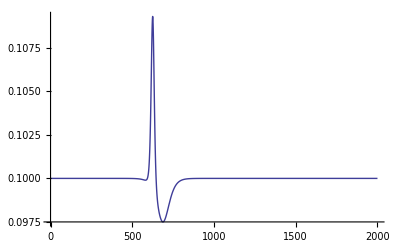

```mathematica
Plot[ρi[x],{x,0,L},PlotRange->All]
```

### equilibrium velocity

```mathematica
ρj=.15; (* veh/m - jaming density *)
v0 = 40; (* m/s - speed limit *)
ve[ρ_]:=v0((1+ⅇ^((ρ/ρj-0.25)/0.06))^-1-3.72 10^-6); (* m/s - equilibrium velocity density relation *)
(*ve[ρ_]:=v0(1-ρ/ρj);*)
```

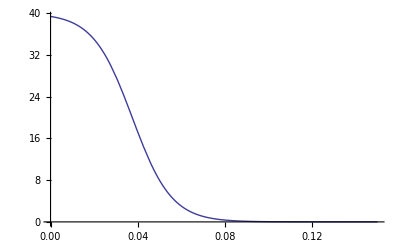

```mathematica
Plot[ve[ρ],{ρ,0,ρj}]
```

### PDE

```mathematica
τ=15; (* s - relaxation time *)
c0 = 15; (* m/s - propagation speed of shock *)
pde={D[ρ[x,t], t]+v[x,t]D[ρ[x,t], x]+ρ[x,t]D[v[x,t], x]==0,D[v[x,t], t]+(v[x,t]-c0)D[v[x,t], x]==(ve[ρ[x,t]]-v[x,t])/τ};
bc={ρ[0,t]==ρ[L,t],v[0,t]==v[L,t]};
ic={ρ[x,0]==ρi[x],v[x,0]==ve[ρi[x]]};
sol=NDSolve[Join[pde,bc,ic],{ρ,v},{x,0,L},{t,0,T}][[1]]
```

{ρ→InterpolatingFunction[{{0.,2000.},{0.,100.}},<>],v→InterpolatingFunction[{{0.,2000.},{0.,100.}},<>]}

```mathematica
(*Animate[
Plot[Evaluate
[ρ[x,t]/.sol],{x,L/4,L},PlotRange->{.9ρ0,1.2ρ0}]
,{t,0,T,1}]
Animate[
Plot[Evaluate
[v[x,t]/.sol],{x,L/4,L},PlotRange->{.9ve[ρ0],1.1ve[ρ0]}]
,{t,0,T,1}]*)
Animate[
Plot[Evaluate
[v[x,t]/.sol],{x,L/4,L},PlotRange->{.9ve[ρ0],1.1ve[ρ0]}]
,{t,0,T,1}]
```